```mathematica
Plot3D[x E^(-(x^2+y^2)),{x,-5,5},{y,-5,5},PlotRange->Full]
```

-Graphics3D-

```mathematica
DensityPlot3D[x E^(-(x^2+y^2+z^2)),{x,-5,5},{y,-5,5},{z,-5,5},ColorFunction->"Rainbow",PlotRange->Full,PlotLegends->Automatic]
```

-Graphics3D-

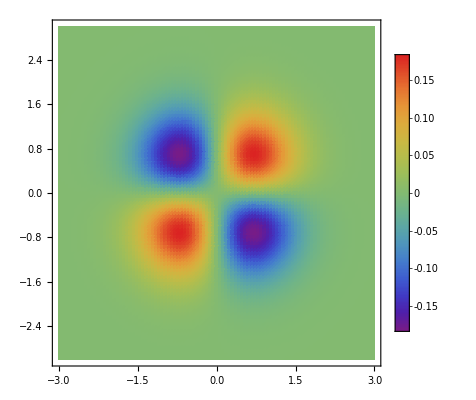

```mathematica
DensityPlot[x y E^(-(x^2+y^2)),{x,-3,3},{y,-3,3},ColorFunction->"Rainbow",PlotPoints->{100,100},PlotRange->Full,PlotLegends->Automatic]
```

```mathematica
E^{-a x^2}/.a->{10,1,0.1}
```

{{ⅇ^(-10 x^2),ⅇ^(-x^2),ⅇ^(-0.1 x^2)}}

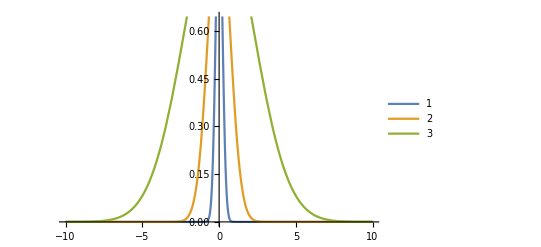

```mathematica
Plot[{ⅇ^(-10 x^2),ⅇ^(-x^2),ⅇ^(-0.1 x^2)},{x,-10,10},PlotLegends->Automatic]
```

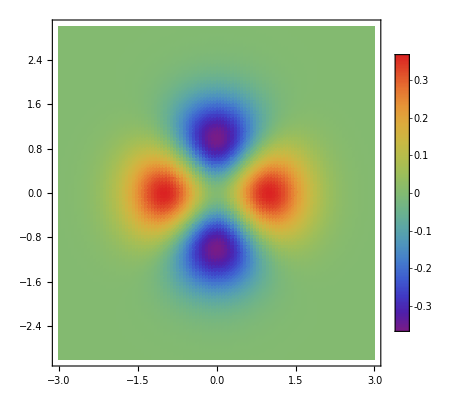

```mathematica
DensityPlot[(x^2-y^2)*E^(-(x^2+y^2)),{x,-3,3},{y,-3,3},ColorFunction->"Rainbow",PlotPoints->{100,100},PlotRange->Full,PlotLegends->Automatic]
```